```mathematica
Ψ[x_] := 1/(Pi^(1/4))*1/(x0^(1/2))*Exp[-1/2*((x-a)/x0)^2]+
1/(Pi^(1/4))*1/(x0^(1/2))*Exp[-1/2*((x+a)/x0)^2];
```

```mathematica
$Assumptions = x0>0&&x0∈Reals && a>0&&a∈Reals&& h>0&&h∈Reals&& m>0&&m∈Reals&& ω>0&&ω∈Reals;
```

```mathematica
H[f_] := -h^2/(2*m)*D[f,{x,2}]+m ω^2/(8*a^2)*(x^2-a^2)^2*f;
```

```mathematica
x0 = (h/(m*ω))^(1/2);
```

```mathematica
Ψ[x]*H[Ψ[x]];
```

```mathematica
ΨEx = Integrate[Ψ[x]*H[Ψ[x]],{x,-∞,∞}];
```

```mathematica
ΨN = Integrate[Ψ[x]*Ψ[x],{x,-∞,∞}];
```

```mathematica
Collect[ΨEx/ΨN,ω]//FullSimplify
```

1/32 h ((3 h)/(a^2 m)+16 ω)+(3 ω (h+a^2 m ω))/(8 (-1+ⅇ^((a^2 m ω)/h)))

```mathematica
ΨEx/ΨN
```

```mathematica
Collect[(ⅇ^(-(a^2 m ω)/h) (3 h^2+4 a^2 h m ω-12 a^4 m^2 ω^2+ⅇ^((a^2 m ω)/h) h (3 h+16 a^2 m ω)))/(16 a^2 (2+2 ⅇ^(-(a^2 m ω)/h)) m),(h ω)/2]
```

(ⅇ^(-(a^2 m ω)/h) (3 h^2+4 a^2 h m ω-12 a^4 m^2 ω^2+ⅇ^((a^2 m ω)/h) h (3 h+16 a^2 m ω)))/(16 a^2 (2+2 ⅇ^(-(a^2 m ω)/h)) m)

```mathematica
Simplify[(ⅇ^(-(a^2 m ω)/h) ω (3 h^2+4 a^2 h m ω-12 a^4 m^2 ω^2+ⅇ^((a^2 m ω)/h) h (3 h+16 a^2 m ω)))/(16 a^2 h √(h/(m ω)) ((m ω)/h)^(3/2))]
```

(ⅇ^(-(a^2 m ω)/h) √(h/(m ω)) √((m ω)/h) (3 h^2+4 a^2 h m ω-12 a^4 m^2 ω^2+ⅇ^((a^2 m ω)/h) h (3 h+16 a^2 m ω)))/(16 a^2 m)

```mathematica
Simplify[(ⅇ^(-(a^2 m ω)/h)  (3 h^2+4 a^2 h m ω-12 a^4 m^2 ω^2+ⅇ^((a^2 m ω)/h) h (3 h+16 a^2 m ω)))/(16 a^2 m)]
```

(ⅇ^(-(a^2 m ω)/h) (3 h^2+4 a^2 h m ω-12 a^4 m^2 ω^2+ⅇ^((a^2 m ω)/h) h (3 h+16 a^2 m ω)))/(16 a^2 m)

```mathematica
Simplify[H[Ψ[x]],Ψ[x]]
```

1/(8 a^2 π^(1/4) (h/(m ω))^(1/4))ⅇ^(-(m (a+x)^2 ω)/(2 h)) ω (-3 a^4 (1+ⅇ^((2 a m x ω)/h)) m ω+8 a^3 (-1+ⅇ^((2 a m x ω)/h)) m x ω+(1+ⅇ^((2 a m x ω)/h)) m x^4 ω+2 a^2 (1+ⅇ^((2 a m x ω)/h)) (2 h-3 m x^2 ω))

```mathematica
Factor[Ψ[x],
```

```mathematica
D[Ψ[x],{x,2}]
```

(-(ⅇ^(-(m (-a+x)^2 ω)/(2 h)) m ω)/h+(ⅇ^(-(m (-a+x)^2 ω)/(2 h)) m^2 (-a+x)^2 ω^2)/h^2)/(π^(1/4) (h/(m ω))^(1/4))+(-(ⅇ^(-(m (a+x)^2 ω)/(2 h)) m ω)/h+(ⅇ^(-(m (a+x)^2 ω)/(2 h)) m^2 (a+x)^2 ω^2)/h^2)/(π^(1/4) (h/(m ω))^(1/4))

```mathematica
H[Exp[-(x/x0)^2]]
```

-(h^2 ((4 ⅇ^(-x^2/x0^2) x^2)/x0^4-(2 ⅇ^(-x^2/x0^2))/x0^2))/(2 m)+(m (-a^2+x^2)^2 ω^2)/(8 a^2)

```mathematica
H0[f_] := -h^2/(2*m)*D[f,{x,2}]+m ω^2/(2)*(x)^2*f;
```

```mathematica
Ψ0[x_] := 1/(Pi^(1/4))*1/(x0^(1/2))*Exp[-1/2*(x/x0)^2];
```

```mathematica
Collect[H0[Ψ0[x]],Ψ0[x]]
```

(ⅇ^(-(m x^2 ω)/(2 h)) m x^2 ω^2)/(2 π^(1/4) (h/(m ω))^(1/4))-(h^2 (-(ⅇ^(-(m x^2 ω)/(2 h)) m ω)/h+(ⅇ^(-(m x^2 ω)/(2 h)) m^2 x^2 ω^2)/h^2))/(2 m π^(1/4) (h/(m ω))^(1/4))

```mathematica
Ψ0[x]
```

(ⅇ^(-(m x^2 ω)/(2 h)))/(π^(1/4) (h/(m ω))^(1/4))

```mathematica
H0[Ψ0[x]]//FullSimplify
```

(ⅇ^(-(m x^2 ω)/(2 h)) h ω)/(2 π^(1/4) (h/(m ω))^(1/4))

```mathematica
D[Exp[-1/2*(x^2-a^2)/x0^2],{x,2}]
```

-(ⅇ^(-(m (-a^2+x^2) ω)/(2 h)) m ω)/h+(ⅇ^(-(m (-a^2+x^2) ω)/(2 h)) m^2 x^2 ω^2)/h^2

```mathematica
Simplify[-(ⅇ^(-(m (-a+x) (a+x) ω)/(2 h)) m ω)/h+ⅇ^(-(m (-a+x) (a+x) ω)/(2 h)) (-(m (-a+x) ω)/(2 h)-(m (a+x) ω)/(2 h))^2]
```

(ⅇ^((m (a-x) (a+x) ω)/(2 h)) m ω (-h+m x^2 ω))/h^2

```mathematica
c= 5;
```

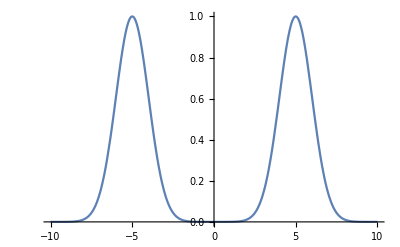

```mathematica
Plot[Exp[-(x-c)^2/2]+Exp[-(x+c)^2/2],{x,-10,10}]
```

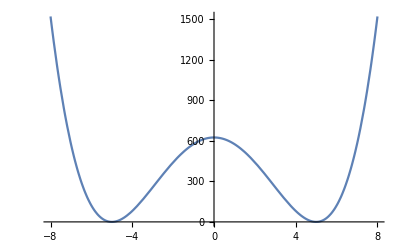

```mathematica
Plot[((x-c)(x+c))^2,{x,-8,8}]
```

```mathematica
Series[(x^2-a^2)^2,{x,-a,4}]
```

4 a^2 (x+a)^2-4 a (x+a)^3+(x+a)^4+O[x+a]^5

```mathematica
Ψ[x]
```

(ⅇ^(-(m (-a+x)^2 ω)/(2 h)))/(π^(1/4) (h/(m ω))^(1/4))-(ⅇ^(-(m (a+x)^2 ω)/(2 h)))/(π^(1/4) (h/(m ω))^(1/4))

```mathematica
ΨEx
```

(ⅇ^(-(a^2 m ω)/h) (3 h^2+4 a^2 h m ω-12 a^4 m^2 ω^2+ⅇ^((a^2 m ω)/h) h (3 h+16 a^2 m ω)))/(16 a^2 m)

```mathematica
ΨN
```

2-2 ⅇ^(-(a^2 m ω)/h)

```mathematica
ΨEx/ΨN//FullSimplify
```

1/32 h ((3 h)/(a^2 m)+16 ω)+(3 ω (h+a^2 m ω))/(8 (-1+ⅇ^((a^2 m ω)/h)))

```mathematica
N[Exp[2]]
```

7.38906